SU(3)

```mathematica
eqn={D[ϕ[u],u,u]== -α ϕ[u] ψ[u]^2-3/4 α ϕ[u] ξ[u]^2,D[ψ[u],u,u]==-α ψ[u] ϕ[u]^2 -3/4 α ψ[u] ξ[u]^2,D[ξ[u],u,u]==-α/4 ξ[u] ϕ[u]^2 -α/4 ξ[u] ψ[u]^2};
ic={ϕ[0]==1,ψ[0]==1,ξ[0]==1};
bc={ϕ'[0]==0,ψ'[0]==0,ξ'[0]==0};
```

```mathematica
α=0.00625;
```

```mathematica
dsol=NDSolve[{eqn,bc,ic},{ϕ,ψ,ξ},{u,0,500},"MaxStepSize"-> 0.005,PrecisionGoal->20]
```

{{ϕ→InterpolatingFunction[{{0., 500.}}, <>],ψ→InterpolatingFunction[{{0., 500.}}, <>],ξ→InterpolatingFunction[{{0., 500.}}, <>]}}

```mathematica
phi=ϕ/.dsol[[1]];
```

```mathematica
psi=ψ/.dsol[[1]];
```

```mathematica
xi=ξ/.dsol[[1]];
```

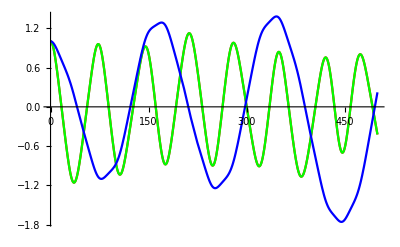

```mathematica
Plot[{phi[u],psi[u],xi[u]},{u,0,500},PlotStyle->{Red,Green,Blue}]
```

```mathematica
DSolve[{D[ϕ[u],u,u]== -α ϕ[u]^3-3/4 α ϕ[u] ξ[u]^2,D[ξ[u],u,u]==-α/2 ξ[u] ϕ[u]^2 },{ϕ,ξ},u]
```

DSolve[{ϕ''[u]==-0.0046875 ξ[u]^2 ϕ[u]-0.00625 ϕ[u]^3,ξ''[u]==-0.003125 ξ[u] ϕ[u]^2},{ϕ,ξ},u]

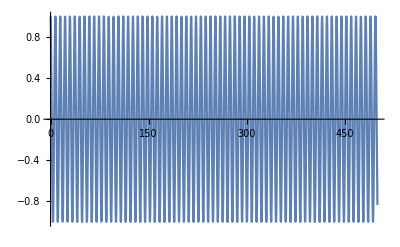

```mathematica
Plot[JacobiCN[u,1/2],{u,0,500}]
```